# Ratio of relative velocity v to the speed of light c in 3D

## In 3D

### Speed of light

```mathematica
c=299792458;
```

### Relative velocity between inertial reference frames

```mathematica
v={0.9c,0,0};
```

```mathematica
Norm[v]
```

2.69813×10^8

### Ratio of relative velocity v to the speed of light c

```mathematica
β[𝓋_]=𝓋/c;
```

```mathematica
β[v]
```

{0.9,0,0}

```mathematica
Norm[β[v]]
```

0.9

```mathematica
βPlot1=Plot[Norm[β[v]],{v,0,c},FrameLabel->{"v (m/s)","β"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic,AspectRatio->1];
```

```mathematica
βPlot2=ListPlot[{{Norm[v],Norm[β[v]]}},MeshStyle->Red,AxesLabel->{"v","Norm[β[v]]"},PlotMarkers->{Automatic,Medium},Frame-> True,GridLines->Automatic,AspectRatio->1];
```

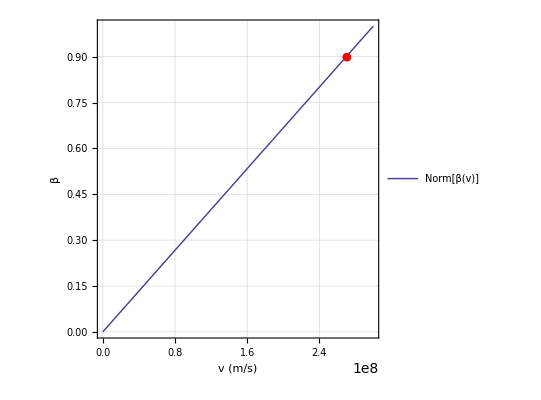

```mathematica
Show[βPlot1,βPlot2]
```